## Transmon Formulas Last version (07-Oct-2009) Modified by FO DO NOT MODIFY !!! -> copy and paste somewhere else !

### Constants

```mathematica
giga=10^9;
mega=10^6;
kilo=1000;
milli=0.001;
nano=10^(-9);
micro=10^(-6);
pico=10^(-12);
femto=10^(-15);
ato=10^(-18);
e=1.6 10^-19;
h=6.62 10^-34;
hbar=h/2./π;
Phi0=h/(2e); 
phi0=hbar/(2e); 
(**  Attention, phi0 est défini avec hbar et non h**)
Z0=50;
```

### Sample Parameters

```mathematica
"Cavity parameters (measured with VNA at low power at 20 mK)";
fcav=6.447 giga;
Q=680;

kappa=κ=2Pi*fcav/Q;

"Transmon parameters";
Ejtot=24.55giga ;
Ec= 1.065 giga ;
d = 0.0;

"Coupling constant";
"Attention : here g denotes the quantity 2βeV(rms,0)";
"The real couplings constants with a physical meaning are then deduced from Ej,Ec and g ( e.g. gij=g|<i|n|j|>| )";
g=35.05mega;
```

### Transmon-Cavity Energy levels

#### Bare transmon (no cavity)

Perturbative Energies of the ib band vs vCoil at the 3 first orders

```mathematica
enpert0[ib_,ec_,ej_]:=ib Sqrt[2 ec ej];
enpert1[ib_,ec_,ej_]:=- (ec/48) (6 ib^2 + 6 ib + 3);
enpert2[ib_,ec_,ej_]:=(ec/48)^2 ( ib (ib-1) (ib-2) (ib-3)/(4 Sqrt[2 ec ej]) + (ib^2-ib) (4 ib-2)^2 / (2 Sqrt[2 ec ej])  
- (ib+1) (ib+2) (4 ib+6)^2 / (2 Sqrt[2 ec ej]) -  (ib+4) (ib+3) (ib+2) (ib+1)/(4 Sqrt[2 ec ej])) +(1/720) (ej)(ec/(2ej))^1.5 ((ib+1) (ib+2) (4 ib + 6) + (2 ib+1) (2 ib^2 + 2 ib +2) + ib (ib-1) (4 ib -2));
enpert[ib_,ec_,ej_]:=enpert0[ib,ec,ej]+enpert1[ib,ec,ej]+enpert2[ib,ec,ej];
```

ib : band index
d is the asymmetry parameter.

Resonance frequency f01 to 0,1,2nd order vs vCoil for a split box of asymmetry parameter d with Josephson energy 
EJ=EJ1 Sqrt[2 + 2 d^2 + 2(1-d^2) Cos[δ]]. Note that if d=0 we recover EJ=2 EJ1 Abs[Cos[δ/2]]. In addition there is a "phenomenological" term Sinc[c vCoil + d2] 
in order to fit the data of run Transmon 1 where there was some flux penetration in the loop. For Transmon 3-5, put c=d2=0
!new version 11/02/08, EJ1 ->EJ1/2 to be consistant with

```mathematica
f01pert0[δ0qb_,ej1_,ec1_]:=Block[{ej2 =.5*ej1*Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]]},(enpert0[1,ec1,ej2]-enpert0[0,ec1,ej2]) / giga];
f01pert1[δ0qb_,ej1_,ec1_]:=Block[{ej2 =.5*ej1* Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]]},(enpert1[1,ec1,ej2]-enpert1[0,ec1,ej2])/ giga+f01pert0[δ0qb,ej1,ec1]];
f01pert2[δ0qb_,ej1_,ec1_]:=Block[{ej2 =.5*ej1* Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]]},(enpert2[1,ec1,ej2]-enpert2[0,ec1,ej2])/giga+f01pert1[δ0qb,ej1,ec1]];
f01pert[δ0qb_,ej1_,ec1_]:=Block[{ej2 =.5*ej1* Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]]},(enpert[1,ec1,ej2]-enpert[0,ec1,ej2])/giga];
```

Resonance frequency f12 to 0, 1, 2 nd order vs vCoil

```mathematica
f12pert0[δ0qb_,ej1_,ec1_]:=Block[{ej2 =.5*ej1* Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]]},(enpert0[2,ec1,ej2]-enpert0[1,ec1,ej2])/ giga];
f12pert1[δ0qb_,ej1_,ec1_]:=Block[{ej2 =.5*ej1* Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]]},(enpert1[2,ec1,ej2]-enpert1[1,ec1,ej2])/ giga+f12pert0[δ0qb,ej1,ec1]];
f12pert2[δ0qb_,ej1_,ec1_]:=Block[{ej2 =.5*ej1* Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]]},(enpert2[2,ec1,ej2]-enpert2[1,ec1,ej2])/ giga+f12pert1[δ0qb,ej1,ec1]];
f12pert[δ0qb_,ej1_,ec1_]:=Block[{ej2 =.5*ej1*  Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]] },(enpert[2,ec1,ej2]-enpert[1,ec1,ej2])/ giga];
```

Plot F01 and (F01+F12)/2 for bare transmon

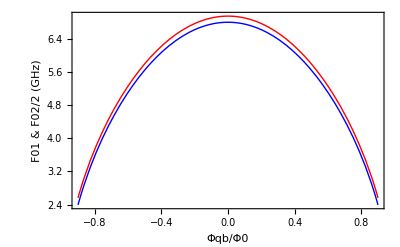

```mathematica
plotF01bare=Plot[f01pert[x,Ejtot,Ec],{x,-.9,.9},PlotRange->All,Axes->None,Frame->True,FrameLabel->{"Φqb/Φ0","F01 & F02/2 (GHz)","Transmon without cavity"},PlotStyle->{Red,Thick},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->14],ImageSize->400];
plothalfF02bare=Plot[(f01pert[x,Ejtot,Ec]+f12pert[x,Ejtot,Ec])/2,{x,-.9,.9},PlotRange->All,Axes->None,Frame->True,FrameLabel->{"Φqb/Φ0","F01 & F02/2 (GHz)","Transmon without cavity"},PlotStyle->{Blue,Thick},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->14],ImageSize->400];
Show[plotF01bare,plothalfF02bare]
```

Anharmi : anharmonicity to i-th order

```mathematica
anharm0[δ0qb_,ej1_,ec1_]:=f12pert0[δ0qb,ej1,ec1]-f01pert0[δ0qb,ej1,ec1];
anharm1[δ0qb_,ej1_,ec1_]:=f12pert1[δ0qb,ej1,ec1]-f01pert1[δ0qb,ej1,ec1];
anharm2[δ0qb_,ej1_,ec1_]:=f12pert2[δ0qb,ej1,ec1]-f01pert2[δ0qb,ej1,ec1];
anharm[δ0qb_,ej1_,ec1_]:=f12pert[δ0qb,ej1,ec1]-f01pert[δ0qb,ej1,ec1];
```

Matrix element |<i|N|i+1>| to zeroth order (i.e harmonic oscillator case. Note that next order is identically 0 so good value)

ATTENTION : Until CJBA4 1st run included, we used an expression with a mistake : (ej/8 ec)^0.25 *Sqrt[ib + 1]

```mathematica
iNip1pert0[ib_,ec_,ej_]:=(ej/8/ec)^0.25 *Sqrt[ib+1];
```

Matrix element  |<0|N|1>| and |<1|N|2>| vs vCoil

```mathematica
N01pert0[δ0qb_,ej1_,ec1_]:=Block[{ej2 =.5*ej1* Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]]},iNip1pert0[0,ec1,ej2]];
N12pert0[δ0qb_,ej1_,ec1_]:=Block[{ej2 =.5*ej1 * Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]]},iNip1pert0[1,ec1,ej2]];
```

#### Dressed states

Coupling constants g01 and g12 vs vCoil (for fixed g01 (0))

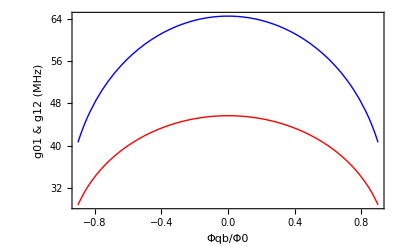

```mathematica
g01[g_,δ0qb_,ej1_,ec1_]:=g Sqrt[N01pert0[δ0qb,ej1,ec1]^2]/giga;
g12[g_,δ0qb_,ej1_,ec1_]:=g Sqrt[N12pert0[δ0qb,ej1,ec1]^2]/giga;
plotg01=Plot[1000*g01[g,x,Ejtot,Ec],{x,-.9,.9},PlotRange->All,Axes->None,Frame->True,PlotStyle->{Red,Thick},ImageSize->400];
plotg02=Plot[1000*g12[g,x,Ejtot,Ec],{x,-.9,.9},PlotRange->All,Axes->None,Frame->True,PlotStyle->{Blue,Thick},ImageSize->400];
Show[plotg01,plotg02,FrameLabel->{"Φqb/Φ0","g01 & g12 (MHz)"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->14]]
```

chiN : Lamb shift of qubit level N due to dispersive interaction with cavity in vacuum 
(VALID ONLY WHEN  |f(N,N+1)-νcav|>>g(N,N+1) (dispersive regime))

```mathematica
chi0[g_,δ0qb_,ej1_,ec1_]:=0;
chi1[g_,δ0qb_,ej1_,ec1_]:=(g01[g,δ0qb,ej1,ec1])^2/(f01pert[δ0qb,ej1,ec1]-fcav/giga);
chi2[g_,δ0qb_,ej1_,ec1_]:=(g12[g,δ0qb,ej1,ec1])^2/(f12pert[δ0qb,ej1,ec1]-fcav/giga);
```

2 chi : frequency shift of the cavity when the qubit goes from |0> to |1>. Also 2chi : shift of the qubit frequency when the cavity contains one photon.

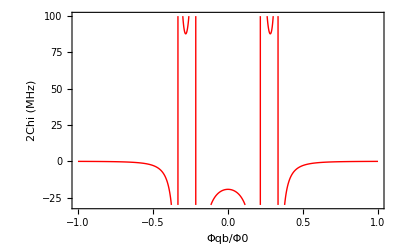

```mathematica
chi[g_,δ0qb_,ej1_,ec1_]:=chi1[g,δ0qb,ej1,ec1]-chi2[g,δ0qb,ej1,ec1]/2;
plotChi=Plot[2chi[g,x,Ejtot,Ec]/0.001,{x,-1,1},PlotRange->{-30,100},Axes->None,Frame->True,FrameLabel->{"Φqb/Φ0","2Chi (MHz)","Cavity pull Vs flux applied to qubit"},PlotStyle->{Red,Thick},ImageSize->400,LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->16]]
```

fNN + 1 disp : qubit transition freq NN+1 Lamb shifted (VALID ONLY IN DISPERSIVE REGIME)

```mathematica
f01disp[g_,δ0qb_,ej1_,ec1_]:=f01pert[δ0qb,ej1,ec1]+chi1[g,δ0qb,ej1,ec1];
f12disp[g_,δ0qb_,ej1_,ec1_]:=f12pert[δ0qb,ej1,ec1]+chi2[g,δ0qb,ej1,ec1]-chi1[g,δ0qb,ej1,ec1];
```

FdressedInf = f01tot : energy of dressed state (nonperturbative) : qubit when f01<<νcav, cav when f01>>νcav

```mathematica
FdressedInf[g_,δ0qb_,ej1_,ec1_]:=0.5*(fcav/giga+f01pert[δ0qb,ej1,ec1])-0.5*Sqrt[(2*g01[g,δ0qb,ej1,ec1])^2+(fcav/giga-f01pert[δ0qb,ej1,ec1])^2];
FdressedInf2[g_,δ0qb_,ej1_,ec1_,n_]:=0.5*(fcav/giga+f01pert[δ0qb,ej1,ec1])-0.5*Sqrt[(n+1)(2*g01[g,δ0qb,ej1,ec1])^2+(fcav/giga-f01pert[δ0qb,ej1,ec1])^2];
```

Fcavdisp = νcavdisp :  cavity frequency shifted by qubit VALID IN DISPERSIVE LIMIT

```mathematica
Fcavdisp[g_,δ0qb_,ej1_,ec1_]:=fcav/giga-chi1[g,δ0qb,ej1,ec1];
```

FdressedSup = νcavtot : energy of dressed state (nonperturbative) : cav when f01 << νcav, qubit when f01 >> νcav

```mathematica
FdressedSup[g_,δ0qb_,ej1_,ec1_]:=0.5*(fcav/giga+f01pert[δ0qb,ej1,ec1])+0.5*Sqrt[(2*g01[g,δ0qb,ej1,ec1])^2+(fcav/giga-f01pert[δ0qb,ej1,ec1])^2];
FdressedSup2[g_,δ0qb_,ej1_,ec1_,n_]:=0.5*(fcav/giga+f01pert[δ0qb,ej1,ec1])+0.5*Sqrt[(n+1)(2*g01[g,δ0qb,ej1,ec1])^2+(fcav/giga-f01pert[δ0qb,ej1,ec1])^2];
```

Critical number of photons in dispersive regime

```mathematica
ncrit[g_,δ0qb_,ej1_,ec1_]:=(FdressedInf[g,δ0qb,ej1,ec1]-FdressedSup[g,δ0qb,ej1,ec1])^2/4/(g01[g,δ0qb,ej1,ec1])^2;
```

Plot Spectro Dressed states

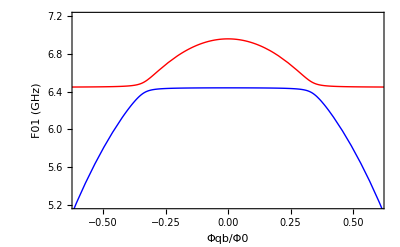

```mathematica
g=45mega;
plotFdressedInf=Plot[FdressedInf[g,x,Ejtot,Ec],{x,-.9,.9},PlotRange->All,Axes->None,Frame->True,FrameLabel->{"Φqb/Φ0","F01 (GHz)","Qubit in cavity : dressed states"},PlotStyle->{Blue,Thick},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->14],ImageSize->400];
plotFdressedSup=Plot[FdressedSup[g,x,Ejtot,Ec],{x,-.9,.9},PlotRange->All,Axes->None,Frame->True,FrameLabel->{"Φqb/Φ0","F01 (GHz)","Qubit in cavity : dressed states"},PlotStyle->{Red,Thick},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->14],ImageSize->400];
plotFdressed=Show[plotFdressedInf,plotFdressedSup,PlotRange->{{-0.6,0.6},{5.2,7.20}}]
```

f12tot : energy of dressed state (nonperturbative) : qubit when f12 << νcav, cav when f12 >> νcav

```mathematica
Clear[H,diag,Energies,E1,E2,E3,F12dressedSup,F12dressedInf];
H[g_,δ0qb_,ej1_,ec1_]:=
{{2fcav/giga, Sqrt[2]*g01[g,δ0qb,ej1,ec1], 0}, {Sqrt[2]*g01[g,δ0qb,ej1,ec1], fcav/giga+f01pert[δ0qb,ej1,ec1], Sqrt[1]*g12[g,δ0qb,ej1,ec1]}, {0, Sqrt[1]*g12[g,δ0qb,ej1,ec1], f01pert[δ0qb,ej1,ec1]+f12pert[δ0qb,ej1,ec1]}};
diag[g_,δ0qb_,ej1_,ec1_]:=Sort[Transpose[Eigensystem[H[g,δ0qb,ej1,ec1]]]];
Energies[g_,δ0qb_,ej1_,ec1_]:=Re[Transpose[diag[g,δ0qb,ej1,ec1]][[1]]];E1[g_,δ0qb_,ej1_,ec1_]:=Energies[g,δ0qb,ej1,ec1][[1]];
E2[g_,δ0qb_,ej1_,ec1_]:=Energies[g,δ0qb,ej1,ec1][[2]];
E3[g_,δ0qb_,ej1_,ec1_]:=Energies[g,δ0qb,ej1,ec1][[3]];
F12dressedSup[g_,δ0qb_,ej1_,ec1_]:=E3[g,δ0qb,ej1,ec1]-FdressedSup[g,δ0qb,ej1,ec1];
F12dressedInf[g_,δ0qb_,ej1_,ec1_]:=E1[g,δ0qb,ej1,ec1]-FdressedInf[g,δ0qb,ej1,ec1];
```

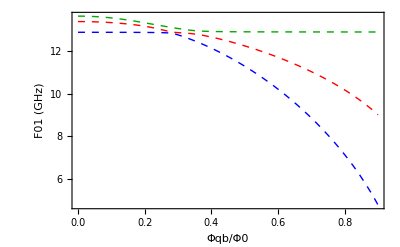

```mathematica
g=45mega;
Plot[{E1[g,x,Ejtot,Ec],E2[g,x,Ejtot,Ec],E3[g,x,Ejtot,Ec]},{x,0,0.9},PlotRange->All,Axes->None,Frame->True,FrameLabel->{"Φqb/Φ0","F01 (GHz)"},PlotStyle->{{Blue,Thick,Dashed},{Red,Thick,Dashed},{Darker[Green],Thick,Dashed}},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->14],ImageSize->400]
```

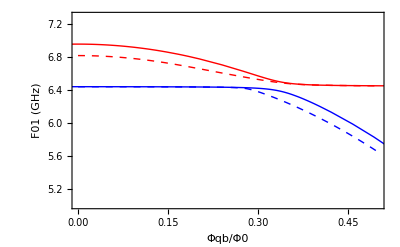

```mathematica
g=45mega;
plotF12dressedSup=Plot[(FdressedSup[g,x,Ejtot,Ec]+F12dressedSup[g,x,Ejtot,Ec])/2,{x,0,0.5},PlotRange->All,Axes->None,Frame->True,PlotStyle->{Red,Thick,Dashed}];
plotF12dressedInf=Plot[(FdressedInf[g,x,Ejtot,Ec]+F12dressedInf[g,x,Ejtot,Ec])/2,{x,0,0.5},PlotRange->All,Axes->None,Frame->True,PlotStyle->{Blue,Thick,Dashed}];
grF12dressed=Show[plotF12dressedSup,plotF12dressedInf,plotFdressed,PlotRange->{{0,0.5},{5,7.3}},FrameLabel->{"Φqb/Φ0","F01 (GHz)","Dressed F01 and F02/2"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->14],ImageSize->400]
```

chiND : chi NON DISPERSIVE VALID ONLY IN THE REGIME WHERE fq<fcav. ChiND=E(11)-E(10)-(E(01)-E(00))

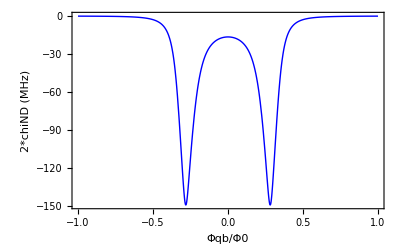

```mathematica
chiND[g_,δ0qb_,ej1_,ec1_]:=(E2[g,δ0qb,ej1,ec1]-FdressedInf[g,δ0qb,ej1,ec1]-FdressedSup[g,δ0qb,ej1,ec1])/2;
plotChiND=Plot[2*chiND[g,x,Ejtot,Ec]/0.001,{x,-1,1},PlotRange->All,Axes->None,Frame->True,FrameLabel->{"Φqb/Φ0","2*chiND (MHz)","2Chi Non Dispersive"},PlotStyle->{Blue,Thick},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->16],ImageSize->400]
```

#### Non Linear AC-Stark shift

In this subsection we calculate the frequency shift of the fundamental transition of the transmon as the cavity is populated with photons even for small detunings where the dispersive approximation breaks

The transmon is modeled as a anharmonic oscillator (with quartic term only) with n=levelsnumber states (up to 5 or 6 for the routine to work)
The cavity is modeled as a harmonic oscillator with n=nmax photons (no limitation).
The coupling is the regular Jaynes-Cummings coupling term.
The Hamiltonian is diagonalized in a basis (| qubitlevel, photon number>) , the eigenenergies ordered, and the function "shift(n)" returns F01(n)-F01(n=0)
An effective cavity pull "chi" is deduced from this shift.

f01 is the fundamental frequency of the qubit in zero field in GHz

```mathematica
Ec/4/2/giga
fcav
```

0.133125

6.447×10^9

```mathematica
chiOrshift[f01_,levelsnumber_,nmax_,chiFlag_:True]:=
Block[
{ subst,qmax=levelsnumber-1, eps=0.5/(nmax+1),
size, en0, en0sort, indices,t1,t0,h0exp,en0list,enqb1,enqb0,eref,hc1,hc2,hc,hcexp, enc, shift, chi,n1,n2},
subst={ωc->fcav/giga,ωq->f01+Ec/4/2/giga,α->Ec/4/2/giga,  gg->g/giga};
size= (qmax+1)(nmax+1);
n1[k_]=Floor[ (k-eps)/(nmax+1)];
n2[k_]=k-(nmax+1)n1[k]-1;
 en0=Table[{n1[i],n2[i],(ωq n1[i]- α  n1[i]^2+ωc n2[i])/.subst},{i,1,size}];
en0sort=Sort[en0, #1[[3]]<#2[[3]]&] ;
indices=Table[ {en0sort[[i]][[1]], en0sort[[i]][[2]]}, {i,1,size}] ;
t1=Table [Position[indices,{1,i} ][[1,1]], {i,0,nmax} ]  ; 
t0=Table [Position[indices,{0,i} ][[1,1]], {i,0,nmax } ]  ;
h0exp =(DiagonalMatrix [Table[en0[[i]][[3]],{i,1,size}]]  //Normal )/.subst ;
en0list=Sort[Eigenvalues[h0exp ]] ;  
    enqb1 =Table[en0list[[t1[[i]]]], {i,1,nmax+1 }];
enqb0=Table[en0list[[t0[[i]]]], {i,1,nmax+1 }] ;
eref=enqb1[[1]]-enqb0[[1]];
hc1=SparseArray[{{i_,j_}/;(j==i +nmax)->gg((n1[i]+1)n2[i])^(1/2)},{size,size}] ;
hc2=Transpose[hc1];
hc=h0exp+hc1+hc2;
hcexp= Normal[hc]/.subst;
MatrixForm[hcexp];
enc=Sort[Eigenvalues[hcexp]];
shift=Table[{i-1,(enc[[t1[[i]]]]-enc[[t0[[i]]]]-eref)}, {i,1,nmax+1}] ;
chi=Table[{i-1, -1000*(shift[[i,2]]-shift[[1,2]])/(2(i-1))}, {i,2,nmax+1}] ; 
If[chiFlag,chi,shift]
]
```

```mathematica
chiPlot[f01_,levelsnumber_,nmax_,color_]:=
Block[{myList=chiOrshift[f01,levelsnumber,nmax,True],Delta=(fcav/giga-f01)/0.001},ListPlot[Drop[myList,-1],PlotStyle->{color},PlotMarkers->{Automatic,Small}, Frame->True,Axes->False,PlotRange->All,ImageSize->400,LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->14], FrameLabel->{"photon number","χ=ΔfAC/(2n) (MHz)", "Delta="<>ToString[Delta]<>"MHz" } ] ]
shiftPlot[f01_,levelsnumber_,nmax_,color_]:=
Block[{myList=chiOrshift[f01,levelsnumber,nmax,False],Delta=(fcav/giga-f01)/0.001},ListPlot[Drop[myList,-1],PlotStyle->{color},PlotMarkers->{Automatic,Small}, Frame->True,Axes->False,PlotRange->All,ImageSize->400,LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->14], FrameLabel->{"photon number","ΔfAC (GHz)","Delta="<>ToString[Delta]<>"MHz"}]]
```

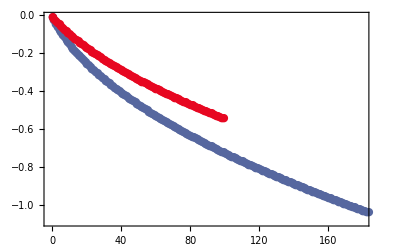

```mathematica
Show[Table[shiftPlot[6.25,i,200,ColorData[i,"ColorList"]],{i,2,6}],PlotRange->{{-1,180},All}]
```

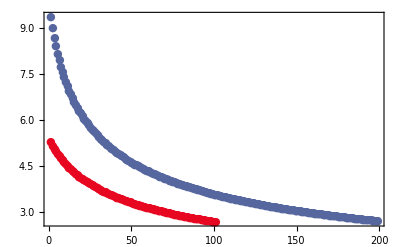

```mathematica
Show[Table[chiPlot[6.25,i,200,ColorData[i,"ColorList"]],{i,2,6}],PlotRange->{{0,180},{0,All}}]
```

Creation of a formula to convert directly the shift in MHz into a photon number in the resonator

```mathematica
Clear[x,a,b,c,d]
offset=Drop[chiOrshift[5.05714,4,300,False],-1][[1,2]];
tabShift=
Map[{-1000(#[[2]]-offset),#[[1]]}&,Drop[chiOrshift[5.05714,4,300,False],-1]];
plotShift=ListPlot[tabShift,Axes->None,Frame->True,PlotRange->All,FrameLabel->{"Shift (MHz)","Nbar"}];
modelpoly=a+b x+c x^2 +d x^3;
fit=FindFit[tabShift,modelpoly,{a,b,c,d},x];
plotfit=Plot[modelpoly/.fit,{x,0,150},PlotStyle->{Thick,Darker[Green]}];
modelpoly/.fit
Show[plotShift,plotfit]
nbarVsShiftMHz[x_]:=modelpoly/.fit
```

### Relaxation and Dephasing

T1 due to Purcell effect (spontaneous emission) for qubit in state |01>
plus additionnal saturating value of T1 called "T1limit"

```mathematica
T1[g_,δ0qb_]:=1/(κ*(g01[g,δ0qb]^2/(f01tot[g,δ0qb]-νcavtot[g,δ0qb])^2)+1/T1limit);
```

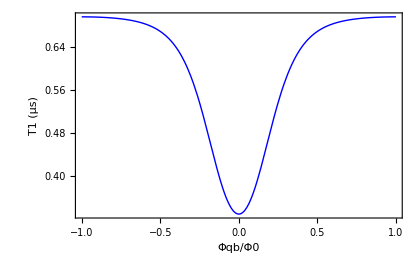

```mathematica
T1limit=700nano;
Plot[{T1[g,δ]}/micro,{δ,-1,1},PlotRange->All,Axes->None,Frame->True,PlotStyle->{Blue,Thick},FrameLabel->{"Φqb/Φ0","T1 (µs)"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->16]]
```

T2 due to charge noise a): fast and small fluctuations;  S_Ng(omega)=2*Pi*A^2/|omega|^µ in the approx. µ=1; with epsilon_m: total charge dispersion epsilon_m=|Em(ng=0)-Em(ng=1)|

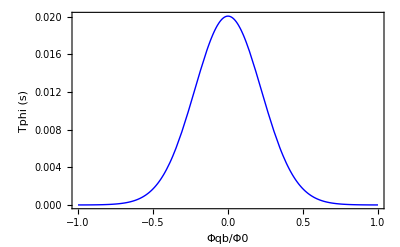

```mathematica
Abnc=10^-3;
T2BCN[δ0qb_]:=Block[{ej2,epsilon1},
ej2 =.5*ej1* Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]] ;epsilon1=ec1/4*2^(4+5)/1!*Sqrt[2/Pi]*(ej2/(2*(ec1/4)))^(1/2+3/4)*E^(-Sqrt[8*ej2/(ec1/4)]);h/2/Pi^2/Abnc/(Abs[epsilon1*h])];
plotT2chargeA=Plot[T2BCN[x],{x,-1,1},PlotRange->All,Axes->None,Frame->True,PlotStyle->{Blue,Thick},FrameLabel->{"Φqb/Φ0","Tphi (s)","ChargeNoise-fast&small"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->16],ImageSize->400]
```

T2 due to charge noise b)  slow and larges fluctuations;

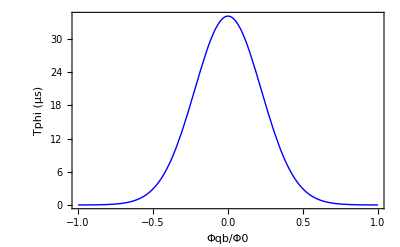

```mathematica
T2BCN2[δ0qb_]:=Block[{ej2,epsilon1},
ej2 =.5*ej1* Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]];epsilon1=ec1/4*2^(4+5)/1!*Sqrt[2/Pi]*(ej2/(2*(ec1/4)))^(1/2+3/4)*E^(-Sqrt[8*ej2/(ec1/4)]);
2*h/Pi/E^2/(Abs[epsilon1*h])];
plotT2chargeB=Plot[T2BCN2[x]*10^6,{x,-1,1},PlotRange->All,Axes->None,Frame->True,PlotStyle->{Blue,Thick},FrameLabel->{"Φqb/Φ0","Tphi (µs)","ChargeNoise-slow&large"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->16],ImageSize->400]
```

T2 due to Fluctuations of Josephson energy a): QBit flux noise; in the general (non symetric) case : T2~hbar/A/|dE01/d(Phi/Phi0)|

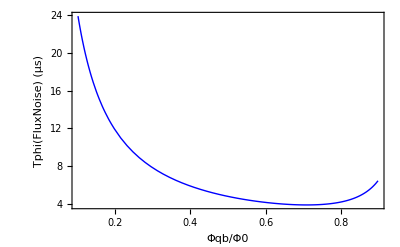

```mathematica
Aflux=10^-5;
Df01tot[g_,δ0qb_]:=Block[{blabla=D[f01tot[g,u]giga,u],u=δ0qb},blabla];
Dνcavtot[g_,δ0qb_]:=Block[{blabla=D[νcavtot[g,u]giga,u],u=δ0qb},blabla];
DF01[g_,δ0qb_]:=Max[Abs[Df01tot[g,δ0qb]],Abs[Dνcavtot[g,δ0qb]]];
T2fluxQB[g_,δ0qb_]:=1/2/Pi/Aflux/DF01[g,δ0qb];
plotT2fluxQB=Plot[T2fluxQB[g,x]/micro,{x,.1,.9},PlotRange->All,Axes->None,Frame->True,PlotStyle->{Blue,Thick},FrameLabel->{"Φqb/Φ0","Tphi(FluxNoise) (µs)"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->16],ImageSize->400]
```

Fluctuations of Josephson energy b): critical current noise (spatial reconfigurations of ions in the tunneling junctions)

```mathematica
Aic=10^-6;
T2Ic[δ0qb_]:=Block[{ej2 =.5*ej1* Sqrt[2+2 d^2+2 (1-d^2) Cos[π δ0qb]]},1/Pi^2/Aic/(f01pert[δ0qb]*giga)];
```

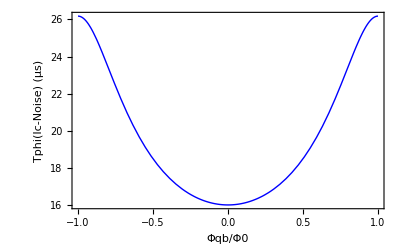

```mathematica
plotT2Ic=Plot[T2Ic[x]/micro,{x,-1,1},PlotRange->All,Axes->None,Frame->True,PlotStyle->{Blue,Thick},FrameLabel->{"Φqb/Φ0","Tphi(Ic-Noise) (µs)"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->16], ImageSize->400]
```

Pure dephasing time Tphi ( 1/Tphi = 1/(1/T2phiQb + 1/T2phiJBA + 1/T2Ic) )

```mathematica
Tphitot[g_,δ0qb_]:=1/(1/T2fluxQB[g,δ0qb]+1/T2Ic[δ0qb]+1/T2BCN[δ0qb]+1/T2BCN2[δ0qb]);
```

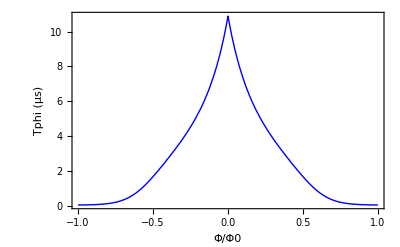

```mathematica
plotTphitot=Plot[Tphitot[g,x]/micro,{x,-1,1},PlotRange->All,Axes->None,Frame->True,FrameLabel->{"Φ/Φ0","Tphi (µs)","Pure Dephasing time"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->16],PlotStyle->{Blue,Thick},ImageSize->400]
```

T2 Ramsey ( 1/T2 = 1/(1/2T1+1/Tphitot) )

```mathematica
T2ramsey[g_,δ0qb_]:=1/(1/2/T1[g,δ0qb]+1/Tphitot[g,δ0qb]);
```

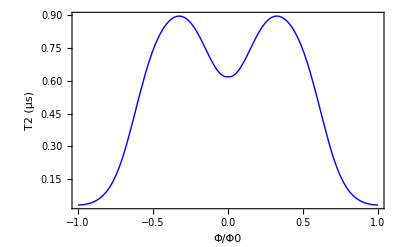

```mathematica
plotT2=Plot[T2ramsey[g,x]/micro,{x,-1,1},PlotRange->All,Axes->None,Frame->True,FrameLabel->{"Φ/Φ0","T2 (µs)","Ramsey coherence time"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->16],PlotStyle->{Blue,Thick},ImageSize->400]
```

Dephasing Rates : bilan

```mathematica
"Main plot options";
plotRateRamsey=LogPlot[{1/T2ramsey[g,δ]}/10^6,{δ,0,1},PlotRange->{0.001,30},Axes->None,Frame->True,PlotStyle->{Magenta,Thick},FrameLabel->{"Φqb/Φ0","Γ (MHz)","Dephasing rates per channel"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->20],ImageSize->800 ];

plotRateRelax=LogPlot[{1/2/T1[g,δ]}/10^6,{δ,0,1},PlotStyle->{Blue,Thick}];

plotRateCN=LogPlot[{1/T2BCN[δ]}/10^6,{δ,0,1},PlotStyle->{Red,Thick}];

plotRateCN2=LogPlot[{1/T2BCN2[δ]}/10^6,{δ,0,1},PlotStyle->{Orange,Thick}];

plotRateQfFlux=LogPlot[{1/T2fluxQB[g,δ]}/10^6,{δ,0,1},PlotStyle->{Darker[Green],Thick}];

plotRateIc=LogPlot[{1/T2Ic[δ]}/10^6,{δ,0,1},PlotStyle->{Purple,Thick}];

plotRateTotal=LogPlot[{1/Tphitot[g,δ]}/10^6,{δ,0,1},PlotStyle->{Black,Thick}];

g0=Show[plotRateRamsey,plotRateTotal,plotRateIc,plotRateQfFlux,plotRateCN2,plotRateCN,plotRateRelax];
```

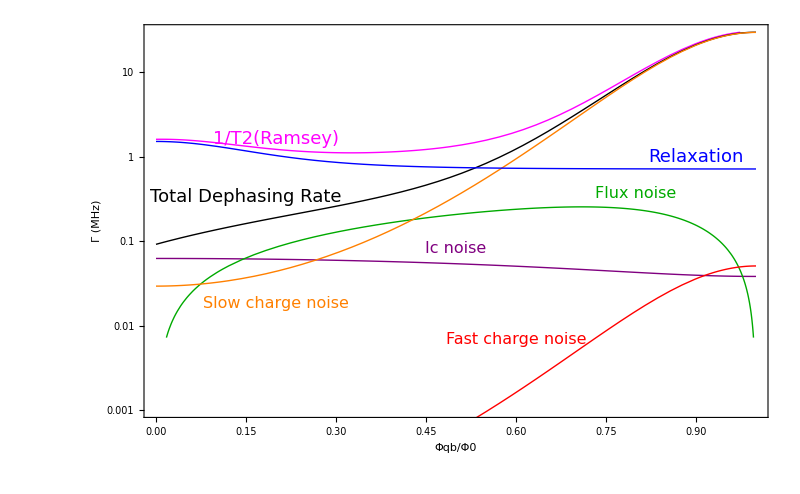

```mathematica
"Labels";
g1=Graphics[{Text[Style["Relaxation",FontFamily->"Arial",FontSize->18,Blue],{0.9,0}],Text[Style["1/T2(Ramsey)",FontFamily->"Arial",FontSize->18,Magenta],{0.2,0.5}],Text[Style["Total Dephasing Rate",FontFamily->"Arial",FontSize->18,Black],{0.15,-1.1}],Text[Style["Flux noise",FontFamily->"Arial",FontSize->16,Darker[Green]],{0.8,-1}],Text[Style["Slow charge noise",FontFamily->"Arial",FontSize->16,Orange],{0.2,-4}],Text[Style["Fast charge noise",FontFamily->"Arial",FontSize->16,Red],{0.6,-5}],Text[Style["Ic noise",FontFamily->"Purple",FontSize->16,Purple],{0.5,-2.5}]},Frame->True];

Show[g0,g1]
```